62/(62+s)

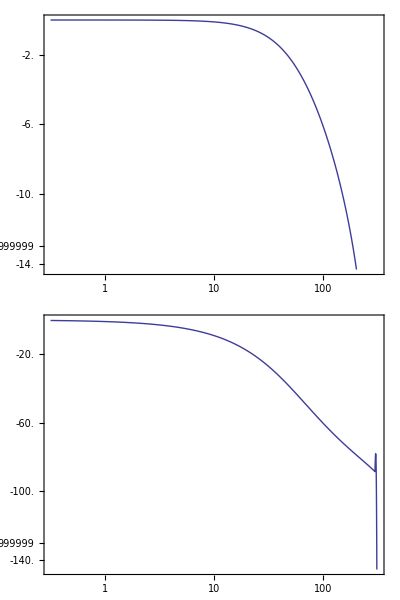

752

```mathematica
ClearAll["Global`*"]

SetOptions[{Plot,ParametricPlot, ListLinePlot, ListPlot},BaseStyle->{FontFamily->"Latin Modern Roman"}];
breakfreq = IntegerPart[10*2*Pi];
sr = 100;



ButterworthFilterModel[{1, breakfreq}, s]
tf = ToDiscreteTimeModel[%, 1/sr, z];
BodePlot[tf]

(*unsigned long ret=(breakfreq*(((unsigned long)s->xp)+((unsigned long)x))-s->yp*(breakfreq-2*hz))/(breakfreq+2*hz);*)

data = Transpose[Import["~/kandikod/measure/samples2.tsv"]];
samples = Length[data[[1]]]
index = PlotLegends-> (Style [#, FontSize -> 10, FontFamily->"Latin Modern Roman"]& /@ {"Tumme 0", "Tumme 1", "Pekfinger 0", "Pekfinger 1", "Långfinger 0", "Långfinger 1"});
range = {PlotRange -> {0, 1023}, DataRange->{0, (samples-1)/sr}, AxesLabel->{"Tid (s)", "f(t)"}};

totdft = Total[Fourier /@ data];
(*totdft = Fourier[data[[1]]];
*)
p0 = ListPlot[
2*Abs[totdft]/samples
, DataRange->{0,  sr}
, PlotRange->{{0, sr/2}, {0, 1}}
, ImageSize->418
, Joined->True
,AxesLabel->{"Hz", "|Y(f)|"}
, Filling->Axis
]




p1 = ListLinePlot[data, range, ImageSize->418]

filtered = RecurrenceFilter[tf, #] & /@ data;
unitResponse = RecurrenceFilter[tf, Array[UnitStep,  sr]];

p2 = ListLinePlot[filtered,  range, ImageSize->418]

ListLinePlot[{data[[4]], filtered[[4]]}, PlotRange -> {{3,4},{1, 1023}}, DataRange->{0, (samples-1)/sr}, AxesLabel->{"Tid (s)", "f(t)"}]

p1 =  ListLinePlot[unitResponse, ImageSize->418, DataRange->{0, 1000},AxesOrigin->{0,0}, AxesLabel->{"Tid (ms)"}, PlotRange->{{0, 100},Full}]

(*Export["flex_raw.pdf", p1]*)
```

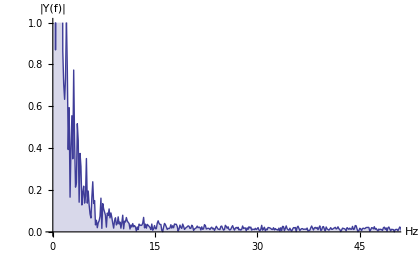

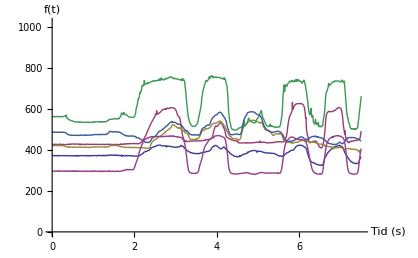

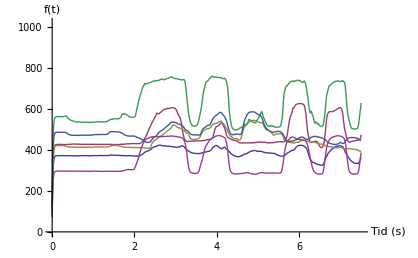

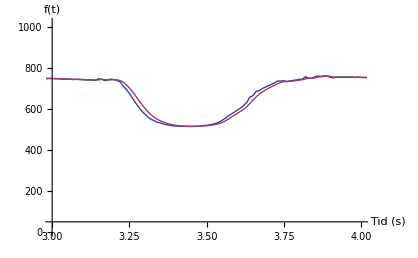

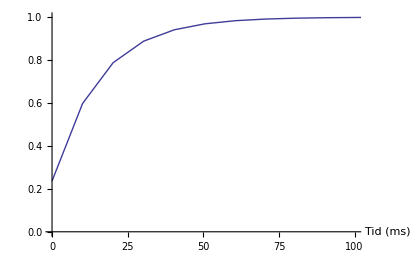

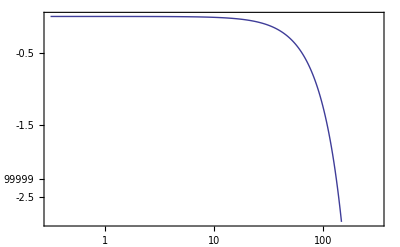
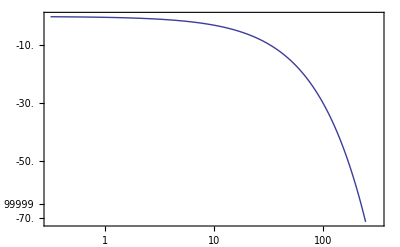

```mathematica
First[%1683]
```